## τα from fitting CRSISF, SISF to stretched exponential

## p0=3.80, N= 512,1024,4096

```mathematica
stretchedExp[t_,G_,τ_,β_]:=G Exp[-(t/τ)^β];
```

```mathematica
TlistNVT={0.002,0.0025,0.0031};
```

```mathematica
TstringNVT=ToString[NumberForm[#,{9,8},ExponentFunction->(Null&)]]&/@TlistNVT
```

{0.00200000,0.00250000,0.00310000}

```mathematica
p0s={3.8}
```

{3.8}

```mathematica
p0sString=ToString[NumberForm[#,{9,3},ExponentFunction->(Null&)]]&/@p0s
```

{3.800}

```mathematica
Ns={512,1024,4096};
```

```mathematica
timeNVT=Table[Table[testdata=Import[StringJoin["/home/chengling/Research/Project/Cell/AnalyticalG/data/N",ToString[Ns[[n]]],"/nvt_N",ToString[Ns[[n]]],"_p3.800_T",TstringNVT[[i]],"_0.nc"],"Data"];Table[testdata[[4,j,1]]-testdata[[4,1,1]],{j,Length[testdata[[4]]]}],{n,3}],{i,Length[TstringNVT]}];
```

```mathematica
CRSISFDifferentN=Table[Table[Import[StringJoin["/home/chengling/Research/Project/Cell/AnalyticalG/data/N",ToString[Ns[[n]]],"/nvt_CRSISF_N",ToString[Ns[[n]]],"_p3.800_T",TstringNVT[[i]],"_0.csv"],"CSV"][[1]],{n,3}],{i,Length[TstringNVT]}];
```

```mathematica
SISFN=Table[Table[Import[StringJoin["/home/chengling/Research/Project/Cell/AnalyticalG/data/N",ToString[Ns[[n]]],"/nvt_SISF_N",ToString[Ns[[n]]],"_p3.800_T",TstringNVT[[i]],"_0.csv"],"CSV"][[1]],{n,3}],{i,Length[TstringNVT]}];
```

```mathematica
SISF512=Table[Table[Import[StringJoin["/home/chengling/Research/Project/Cell/AnalyticalG/data/N",ToString[Ns[[1]]],"/nvt_SISF_N",ToString[Ns[[1]]],"_p3.800_T",TstringNVT[[i]],"_",ToString[idx],".csv"],"CSV"][[1]],{idx,0,9}],{i,Length[TstringNVT]}];
```

```mathematica
SISF512Mean=Table[Table[Mean[Table[SISF512[[i,idx]][[time]],{idx,10}]],{time,Length[timeNVT[[i,1]]]}],{i,Length[timeNVT]}];
```

```mathematica
CRSISF512=Table[Table[Import[StringJoin["/home/chengling/Research/Project/Cell/AnalyticalG/data/N",ToString[Ns[[1]]],"/nvt_CRSISF_N",ToString[Ns[[1]]],"_p3.800_T",TstringNVT[[i]],"_",ToString[idx],".csv"],"CSV"][[1]],{idx,0,9}],{i,Length[TstringNVT]}];
```

```mathematica
CRSISF512Mean=Table[Table[Mean[Table[CRSISF512[[i,idx]][[time]],{idx,10}]],{time,Length[timeNVT[[i,1]]]}],{i,Length[timeNVT]}];
```

```mathematica
SISF1024=Table[Table[Import[StringJoin["/home/chengling/Research/Project/Cell/AnalyticalG/data/N",ToString[Ns[[2]]],"/nvt_SISF_N",ToString[Ns[[2]]],"_p3.800_T",TstringNVT[[i]],"_",ToString[idx],".csv"],"CSV"][[1]],{idx,0,2}],{i,Length[TstringNVT]}];
```

```mathematica
SISF1024Mean=Table[Table[Mean[Table[SISF1024[[i,idx]][[time]],{idx,3}]],{time,Length[timeNVT[[i,1]]]}],{i,Length[timeNVT]}];
```

```mathematica
CRSISF1024=Table[Table[Import[StringJoin["/home/chengling/Research/Project/Cell/AnalyticalG/data/N",ToString[Ns[[2]]],"/nvt_CRSISF_N",ToString[Ns[[2]]],"_p3.800_T",TstringNVT[[i]],"_",ToString[idx],".csv"],"CSV"][[1]],{idx,0,2}],{i,Length[TstringNVT]}];
```

```mathematica
CRSISF1024Mean=Table[Table[Mean[Table[CRSISF1024[[i,idx]][[time]],{idx,3}]],{time,Length[timeNVT[[i,1]]]}],{i,Length[timeNVT]}];
```

```mathematica
timeCRSISFDifferentN={Table[Table[{timeNVT[[i,1,rec]],CRSISF512Mean[[i,rec]]},{rec,20,Length[CRSISFDifferentN[[i,1]]]}],{i,Length[timeNVT]}],Table[Table[{timeNVT[[i,1,rec]],CRSISF1024Mean[[i,rec]]},{rec,20,Length[CRSISFDifferentN[[i,1]]]}],{i,Length[timeNVT]}],Table[Table[{timeNVT[[i,1,rec]],CRSISFDifferentN[[i,3,rec]]},{rec,20,Length[CRSISFDifferentN[[i,1]]]}],{i,Length[timeNVT]}]};
```

```mathematica
timeSISFDifferentN={Table[Table[{timeNVT[[i,1,rec]],SISF512Mean[[i,rec]]},{rec,18,Length[CRSISFDifferentN[[i,1]]]}],{i,Length[timeNVT]}],Table[Table[{timeNVT[[i,1,rec]],SISF1024Mean[[i,rec]]},{rec,18,Length[CRSISFDifferentN[[i,1]]]}],{i,Length[timeNVT]}],Table[Table[{timeNVT[[i,1,rec]],SISFN[[i,3,rec]]},{rec,18,Length[CRSISFDifferentN[[i,1]]]}],{i,Length[timeNVT]}]};
```

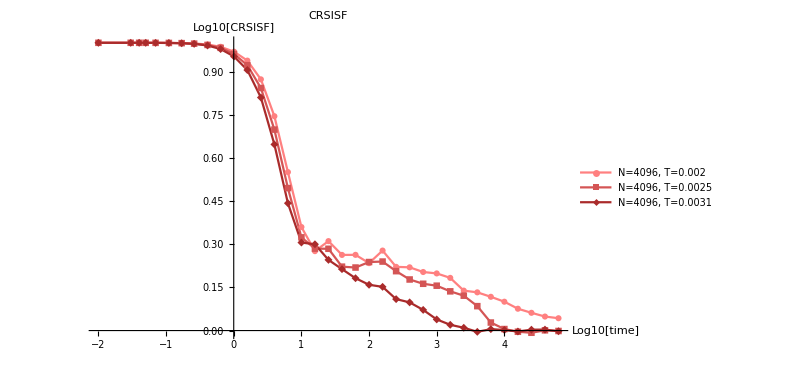

```mathematica
CRSISFPlot=ListLinePlot[Table[Table[{Log10[timeNVT[[i,1,rec]]+0.01],SISF512Mean[[i,rec]]},{rec,Length[CRSISFDifferentN[[i,1]]]}],{i,Length[timeNVT]}],
PlotStyle->Table[Blend[{GrayLevel[1-i/Length[timeNVT]],RGBColor[1,0,0]},0.5],{i,0,Length[timeNVT]}],PlotMarkers->Automatic,PlotLegends->Table[StringJoin["N=4096, T=",ToString[TlistNVT[[i]]]],{i,Length[timeNVT]}],AxesLabel->{"Log10[time]","Log10[CRSISF]"},ImageSize->600,PlotLabel->"CRSISF",PlotRange->Automatic]
```

```mathematica
Length[timeNVT[[1,1]]]
```

35

```mathematica
timeCRSISFDifferentN=Table[Table[Table[{timeNVT[[i,1,rec]],CRSISFDifferentN[[i,n,rec]]},{rec,20,Length[CRSISFDifferentN[[i,1]]]}],{i,Length[timeNVT]}],{n,3}];
```

```mathematica
fit=NonlinearModelFit[timeCRSISFDifferentN[[2]][[1]],{stretchedExp[t,G,τ,β],{1>β>0.01,0<G<1,τ>0}},{G,τ,β},t];
```

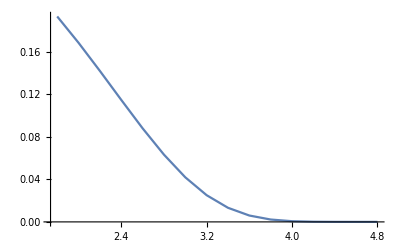

```mathematica
fitPlot=ListLinePlot[Table[{Log10[timeNVT[[1,1,rec]]+0.01],SISFfitsDifferentN[[1]][[3]][timeNVT[[1,1,rec]]]},{rec,20,Length[CRSISFDifferentN[[1,1]]]}]]
```

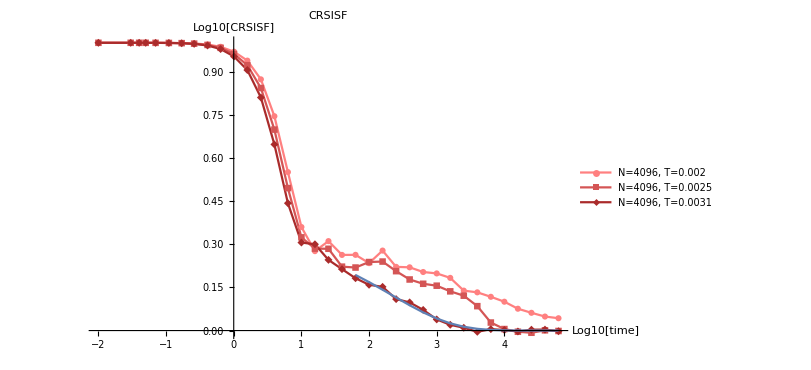

```mathematica
Show[CRSISFPlot,fitPlot]
```

```mathematica
SISFfitsDifferentN[[3]][[1]]["BestFitParameters"]
```

{G→0.999445,τ→10.737,β→0.255685}

```mathematica
Simplify[Log10[A Exp[(-b)^c]]]
```

Log[A ⅇ^((-b)^c)]/Log[10]

```mathematica
timeCRSISFDifferentN[[3]][[3]]
```

{{63.1,0.423591},{100.,0.389313},{158.49,0.347963},{251.19,0.339029},{398.11,0.297434},{630.96,0.257363},{1000.,0.208064},{1584.89,0.133766},{2511.89,0.070347},{3981.07,0.0189599},{6309.57,0.00486076},{10000.,-0.00477611},{15848.9,-0.00480651},{25118.9,-0.00689134},{39810.7,-0.00250884},{63095.7,-0.0016598}}

```mathematica
fitsDifferentN=Table[Table[NonlinearModelFit[timeCRSISFDifferentN[[n]][[T]],{stretchedExp[t,G,τ,β],{1>β>0.01,0<G<1,τ>0}},{G,τ,β},t],{T,3}],{n,3}];
```

```mathematica
SISFfitsDifferentN=Table[Table[NonlinearModelFit[timeSISFDifferentN[[n]][[T]],{stretchedExp[t,G,τ,β],{1>β>0.01,0<G<1,τ>0}},{G,τ,β},t],{T,3}],{n,3}];
```

```mathematica
τCRSISFDN=Table[Table[fitsDifferentN[[n]][[T]]["BestFitParameters"][[2,2]],{T,3}],{n,3}]
```

{{23004.5,5409.22,1843.04},{9566.57,4227.21,1551.34},{4987.84,2078.03,1287.55}}

```mathematica
τSISFDN=Table[Table[SISFfitsDifferentN[[n]][[T]]["BestFitParameters"][[2,2]],{T,3}],{n,3}]
```

{{4419.22,2701.88,213.739},{229.291,935.641,308.564},{13.067,267.384,8.02368}}

```mathematica
Grid[τCRSISFDN]
```

23004.5 | 5409.22 | 1843.04
9566.57 | 4227.21 | 1551.34
4987.84 | 2078.03 | 1287.55

## τ from overlapfunction

```mathematica
overlapN=Table[Table[Import[StringJoin["/home/chengling/Research/Project/Cell/AnalyticalG/data/N",ToString[Ns[[n]]],"/nvt_Overlap_N",ToString[Ns[[n]]],"_p3.800_T",TstringNVT[[i]],"_0.csv"],"CSV"][[1]],{n,3}],{i,Length[TstringNVT]}];
```

```mathematica
ovelap512=Table[Table[Import[StringJoin["/home/chengling/Research/Project/Cell/AnalyticalG/data/N",ToString[Ns[[1]]],"/nvt_Overlap_N",ToString[Ns[[1]]],"_p3.800_T",TstringNVT[[i]],"_",ToString[idx],".csv"],"CSV"][[1]],{idx,0,9}],{i,Length[TstringNVT]}];
```

```mathematica
overlap512Mean=Table[Table[Mean[Table[ovelap512[[i,idx]][[time]],{idx,10}]],{time,Length[timeNVT[[i,1]]]}],{i,Length[timeNVT]}];
```

```mathematica
ovelap1024=Table[Table[Import[StringJoin["/home/chengling/Research/Project/Cell/AnalyticalG/data/N",ToString[Ns[[2]]],"/nvt_Overlap_N",ToString[Ns[[2]]],"_p3.800_T",TstringNVT[[i]],"_",ToString[idx],".csv"],"CSV"][[1]],{idx,0,2}],{i,Length[TstringNVT]}];
```

```mathematica
overlap1024Mean=Table[Table[Mean[Table[ovelap1024[[i,idx]][[time]],{idx,3}]],{time,Length[timeNVT[[i,1]]]}],{i,Length[timeNVT]}];
```

```mathematica
timeOverlapDifferentN={Table[Table[{timeNVT[[i,1,rec]],overlap512Mean[[i,rec]]},{rec,Length[CRSISFDifferentN[[i,1]]]}],{i,Length[timeNVT]}],Table[Table[{timeNVT[[i,1,rec]],overlap1024Mean[[i,rec]]},{rec,Length[CRSISFDifferentN[[i,1]]]}],{i,Length[timeNVT]}],Table[Table[{timeNVT[[i,1,rec]],overlapN[[i,3,rec]]},{rec,Length[CRSISFDifferentN[[i,1]]]}],{i,Length[timeNVT]}]};
```

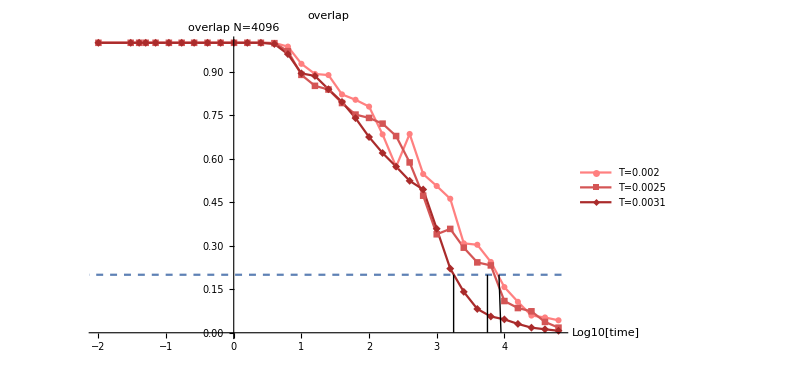

```mathematica
Show[ListLinePlot[Table[Table[{Log10[timeNVT[[i,1,rec]]+0.01],overlapN[[i,3,rec]]},{rec,Length[CRSISFDifferentN[[i,1]]]}],{i,Length[timeNVT]}],
PlotStyle->Table[Blend[{GrayLevel[1-i/Length[timeNVT]],RGBColor[1,0,0]},0.5],{i,0,Length[timeNVT]}],PlotMarkers->Automatic,PlotLegends->Table[StringJoin["T=",ToString[TlistNVT[[i]]]],{i,Length[timeNVT]}],AxesLabel->{"Log10[time]","overlap N=4096"},ImageSize->600,PlotLabel->"overlap",PlotRange->Automatic],Plot[0.2,{x,-10,100},PlotStyle->Dashed],Graphics[Line[{{3.25,0},{3.25,0.2}}]],Graphics[Line[{{3.75,0},{3.75,0.2}}]],Graphics[Line[{{3.95,0},{3.92,0.2}}]]]
```

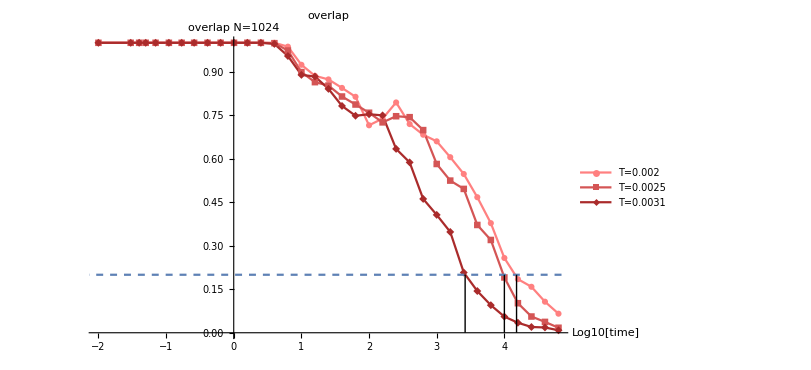

```mathematica
Show[ListLinePlot[Table[Table[{Log10[timeNVT[[i,1,rec]]+0.01],overlap1024Mean[[i,rec]]},{rec,Length[CRSISFDifferentN[[i,1]]]}],{i,Length[timeNVT]}],
PlotStyle->Table[Blend[{GrayLevel[1-i/Length[timeNVT]],RGBColor[1,0,0]},0.5],{i,0,Length[timeNVT]}],PlotMarkers->Automatic,PlotLegends->Table[StringJoin["T=",ToString[TlistNVT[[i]]]],{i,Length[timeNVT]}],AxesLabel->{"Log10[time]","overlap N=1024"},ImageSize->600,PlotLabel->"overlap",PlotRange->Automatic],Plot[0.2,{x,-10,100},PlotStyle->Dashed],Graphics[Line[{{3.42,0},{3.42,0.2}}]],Graphics[Line[{{4.0,0},{4.0,0.2}}]],Graphics[Line[{{4.18,0},{4.18,0.2}}]]]
```

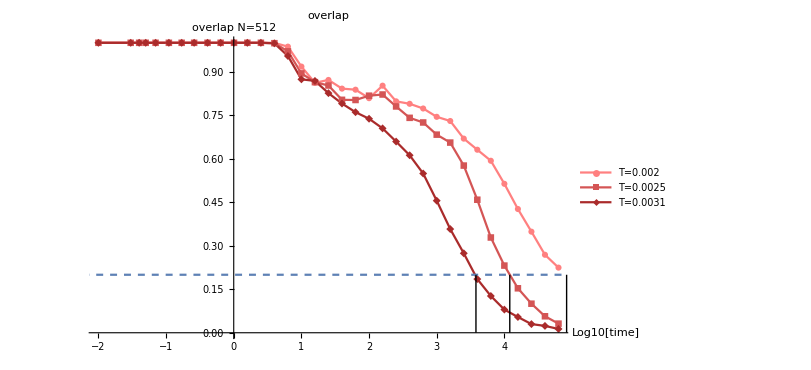

```mathematica
Show[ListLinePlot[Table[Table[{Log10[timeNVT[[i,1,rec]]+0.01],overlap512Mean[[i,rec]]},{rec,Length[CRSISFDifferentN[[i,1]]]}],{i,Length[timeNVT]}],
PlotStyle->Table[Blend[{GrayLevel[1-i/Length[timeNVT]],RGBColor[1,0,0]},0.5],{i,0,Length[timeNVT]}],PlotMarkers->Automatic,PlotLegends->Table[StringJoin["T=",ToString[TlistNVT[[i]]]],{i,Length[timeNVT]}],AxesLabel->{"Log10[time]","overlap N=512"},ImageSize->600,PlotLabel->"overlap",PlotRange->
Automatic],Plot[0.2,{x,-10,100},PlotStyle->Dashed],Graphics[Line[{{3.58,0},{3.58,0.2}}]],Graphics[Line[{{4.08,0},{4.08,0.2}}]],Graphics[Line[{{4.92,0},{4.92,0.2}}]]]
```

```mathematica
ex10[x_]:=10^x;
```

```mathematica
τoverlapDN=ex10/@{{4.92,4.08,3.58},{4.18,4.0,3.42},{3.95,3.75,3.25}}
```

{{83176.4,12022.6,3801.89},{15135.6,10000.,2630.27},{8912.51,5623.41,1778.28}}